```mathematica
Solve[{0==k x-(1+y)a,0==k y-x a},{x,y}]
```

{{x→-(a k)/(a^2-k^2),y→a^2/(-a^2+k^2)}}

```mathematica
Solve[{(c^2 (B-2 x))/((c-x)^2 √(c x))+(4 c (B-2 x) √(c x))/(c-x)^3-(4 c √(c x))/(c-x)^2==0},{x}]
```

{{x→1/4 (3 B-6 c-√(9 B^2-28 B c+36 c^2))},{x→1/4 (3 B-6 c+√(9 B^2-28 B c+36 c^2))}}

```mathematica
(2*c*(c x)^(1/2))*((B-2*x)/((c-x)^2))
```

(2 c (B-2 x) √(c x))/(c-x)^2

```mathematica
D[(2 c (B-2 x) √(c x))/(c-x)^2, x]
```

(c^2 (B-2 x))/((c-x)^2 √(c x))+(4 c (B-2 x) √(c x))/(c-x)^3-(4 c √(c x))/(c-x)^2

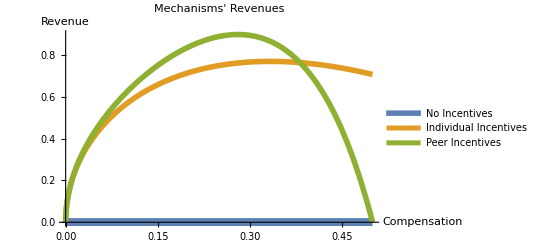

~/Dropbox/Apps/Overleaf/DissertationNYUMignozzetti/figures/figrev.pdf

~/Dropbox/Apps/Overleaf/DissertationNYUMignozzetti/figures/figrev.pdf

```mathematica
RNoI[x_] := 0*x

RInd[x_] := 2(x^(1/2))*(1-x)

RCol[x_] := (2(x^(1/2))*(1-2x))/(1-x)^2

Plot[{RNoI[x],RInd[x],RCol[x]},{x,0,0.5}, PlotLegends->{"No Incentives","Individual Incentives", "Peer Incentives"}, PlotLabel->"Mechanisms' Revenues",PlotStyle->{Thickness[0.015],Thickness[0.01],Thickness[0.01]}, AxesLabel -> {"Compensation","Revenue"}]
Export["~/Dropbox/Apps/Overleaf/DissertationNYUMignozzetti/figures/figrev.pdf",%]
```